```mathematica
styles=Sequence@@{ImageSize->500,Filling->Axis,PlotRange->{0.01,All},AxesOrigin->{-0.01,0.01},PlotStyle->(Directive[AbsoluteThickness[2],#]&/@ColorData[1, "ColorList"])};
```

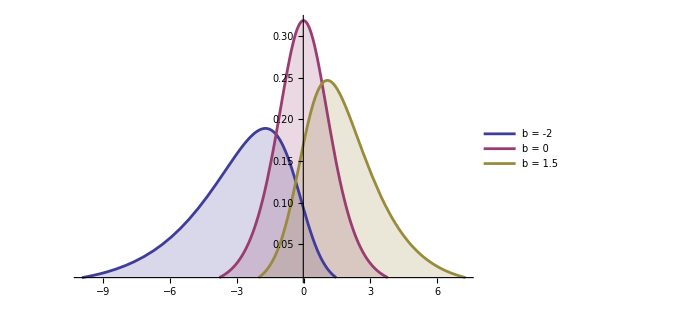

```mathematica
Plot[Evaluate@Table[PDF[MeixnerDistribution[2,b,0,1],x],{b,{-2,0,1.5}}],{x,-10,10},Evaluate@styles,PlotLegends->LineLegend[{"b = -2","b = 0","b = 1.5"}]]
```

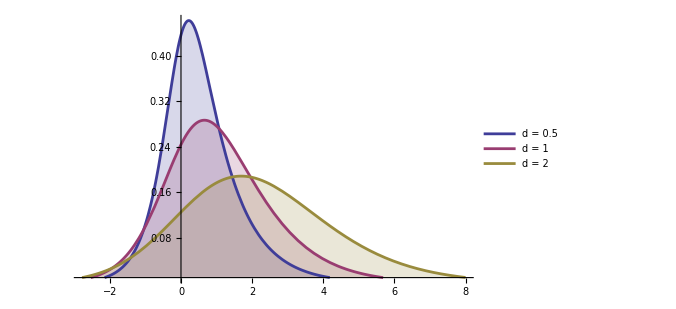

```mathematica
Plot[Evaluate@Table[PDF[MeixnerDistribution[2,1,0,d],x],{d,{0.5,1,2}}],{x,-3,8},Evaluate@styles,PlotLegends->LineLegend[{"d = 0.5","d = 1","d = 2"}]]
```

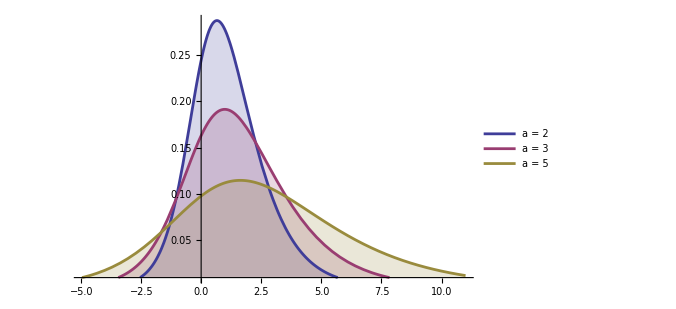

```mathematica
Plot[Evaluate@Table[PDF[MeixnerDistribution[a,1,0,1],x],{a,{2,3,5}}],{x,-5,11},Evaluate@styles,PlotLegends->LineLegend[{"a = 2","a = 3","a = 5"}]]
```

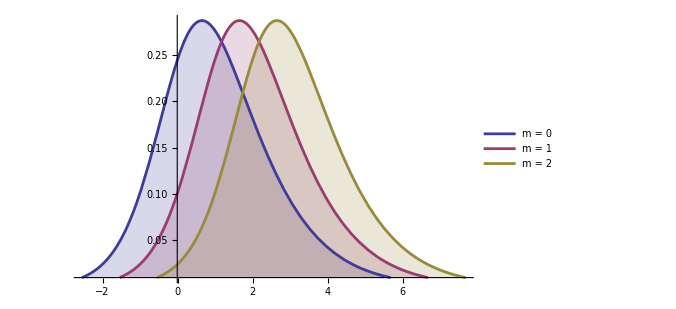

```mathematica
Plot[Evaluate@Table[PDF[MeixnerDistribution[2,1,m,1],x],{m,{0,1,2}}],{x,-3,8},Evaluate@styles,PlotLegends->LineLegend[{"m = 0","m = 1","m = 2"}]]
```

```mathematica
data=RandomVariate[MeixnerDistribution[1,-2,0,3],10^4];
```

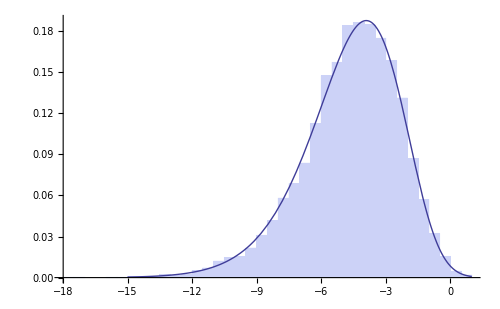

```mathematica
Show[Histogram[data,30,"PDF"],Plot[PDF[MeixnerDistribution[1,-2,0,3],x],{x,-15,1},PlotStyle->Thick],ImageSize->500]
```

```mathematica
data=FinancialData["SP500","Return",{{2000,1,1},{2010,1,1}}][[All,2]];
```

```mathematica
edist=EstimatedDistribution[data,MeixnerDistribution[a,b,m,d],ParameterEstimator->"MethodOfMoments"]
```

MeixnerDistribution[0.0555843,0.0507417,-0.000183754,0.124796]

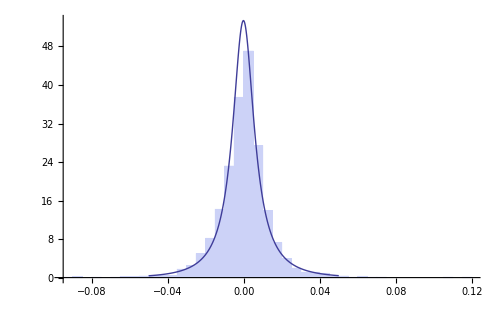

```mathematica
Show[Histogram[data,35,"PDF"],Plot[PDF[edist,x],{x,-0.05,0.05},PlotStyle->Thick],ImageSize->500]
```

```mathematica
edist2=EstimatedDistribution[data,MeixnerDistribution[a,b,m,d],ParameterEstimator->"MaximumLikelihood"]
```

MeixnerDistribution[0.0466282,-0.176725,0.000706459,0.172887]

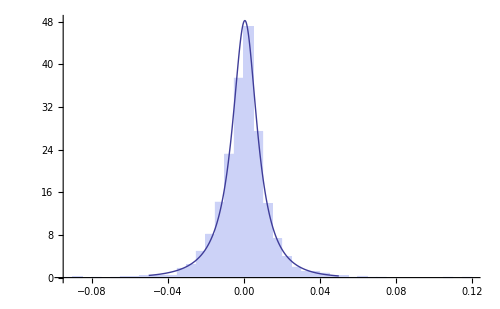

```mathematica
Show[Histogram[data,35,"PDF"],Plot[PDF[edist2,x],{x,-0.05,0.05},PlotStyle->Thick],ImageSize->500]
```